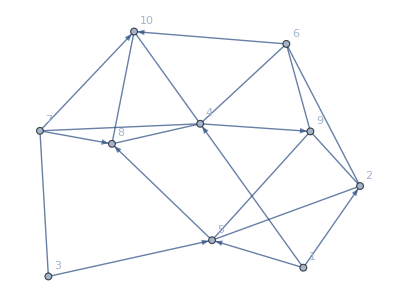

```mathematica
randomWeightedMixedGraph=RandomWeightedMixedGraph[{10,20},0.6,RandomReal[]&,VertexLabels->Automatic]
```

```mathematica
WeightedGraphQ[randomWeightedMixedGraph]
```

True

## Undirected Edges

```mathematica
EdgeList[randomWeightedMixedGraph,_UndirectedEdge]
```

{1<->5,1<->10,2<->3,2<->10,4<->7,5<->6,5<->7,7<->9}

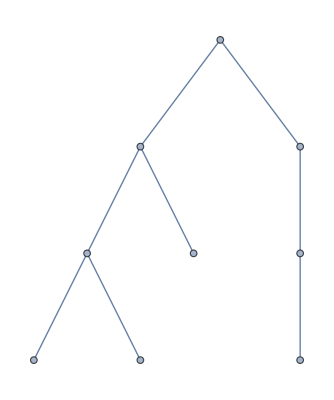

```mathematica
Graph[EdgeList[randomWeightedMixedGraph,_UndirectedEdge]]
```

### WeightedAdjacencyMatrix

```mathematica
WeightedAdjacencyMatrix[Graph[EdgeList[randomWeightedMixedGraph,_UndirectedEdge]]]
```

SparseArray[…]

```mathematica
WeightedAdjacencyMatrix[Graph[EdgeList[randomWeightedMixedGraph,_UndirectedEdge]]]//MatrixForm
```

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

```mathematica
LinearOptimization[Weigh,{},{x∈Matrices[{VertexCount[graph],VertexCount[graph]},Integers]}]
```

### Symmetric Part of Matrix

```mathematica
Symmetrize[WeightedAdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]
```

SymmetrizedArray[…]

```mathematica
First/@SymmetrizedArrayRules@Symmetrize[WeightedAdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]
```

{{1,4},{1,2},{1,5},{2,5},{2,6},{2,9},{3,5},{3,7},{4,9},{4,7},{4,6},{4,8},{4,10},{5,8},{5,9},{6,10},{6,9},{7,8},{7,10},{8,10},{_,_}}

```mathematica
ArrayRules@Symmetrize[WeightedAdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]
```

{{1,2}→0.103394,{1,4}→0.277671,{1,5}→0.286405,{2,1}→0.103394,{2,5}→0.774609,{2,6}→0.0171756,{2,9}→0.71192,{3,5}→0.0605027,{3,7}→0.659459,{4,1}→0.277671,{4,6}→0.350472,{4,7}→0.484129,{4,8}→0.315954,{4,9}→0.418736,{4,10}→0.860338,{5,1}→0.286405,{5,2}→0.774609,{5,3}→0.0605027,{5,8}→0.125694,{5,9}→0.955681,{6,2}→0.0171756,{6,4}→0.350472,{6,9}→0.338789,{6,10}→0.106668,{7,3}→0.659459,{7,4}→0.484129,{7,8}→0.270527,{7,10}→0.471588,{8,4}→0.315954,{8,5}→0.125694,{8,7}→0.270527,{8,10}→0.796248,{9,2}→0.71192,{9,4}→0.418736,{9,5}→0.955681,{9,6}→0.338789,{10,4}→0.860338,{10,6}→0.106668,{10,7}→0.471588,{10,8}→0.796248,{_,_}→0}

```mathematica
EdgeList[randomWeightedMixedGraph,_DirectedEdge]
```

{1->4,1->2,1->5,3->5,4->9,4->7,4->6,5->8,6->10,6->9,7->8,7->10}

```mathematica
WeightedAdjacencyMatrix[randomWeightedMixedGraph][[2,5]]
```

0.774609

```mathematica
WeightedAdjacencyMatrix[randomWeightedMixedGraph][[5,2]]
```

0.774609

```mathematica
TensorSymmetry[({{0, a, b}, {a, 0, c}, {0, c, 0}})]
```

{}

```mathematica
TensorSymmetry[({{0, a, b}, {a, 0, c}, {0, c, 0}}),{1}]
```

{}

```mathematica
TensorSymmetry[({{0, a, b}, {a, 0, c}, {0, c, 0}}),{2,3}]
```

TensorSymmetry::slrank: Second argument, {2,3}, should be a list of different integers not greater than the tensor rank 2.

TensorSymmetry[{{0,a,b},{a,0,c},{0,c,0}},{2,3}]

```mathematica
{({{0, a, b}, {a, 0, c}, {0, c, 0}}),Transpose[({{0, a, b}, {a, 0, c}, {0, c, 0}})]}
```

{{{0,a,b},{a,0,c},{0,c,0}},{{0,a,0},{a,0,c},{b,c,0}}}

```mathematica
Position[{1,2,3.0,4,5},x_?IntegerQ]
```

{{1},{2},{4},{5}}

### Directed Edges Positions

```mathematica
DirectedEdge@@First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]
```

{1->4,1->2,1->5,3->5,4->9,4->7,4->6,5->8,6->10,6->9,7->8,7->10}

```mathematica
EdgeList[randomWeightedMixedGraph,_DirectedEdge]
```

{1->4,1->2,1->5,3->5,4->9,4->7,4->6,5->8,6->10,6->9,7->8,7->10}

```mathematica
First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]
```

{{1,4},{1,2},{1,5},{3,5},{4,9},{4,7},{4,6},{5,8},{6,10},{6,9},{7,8},{7,10}}

```mathematica
WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"]
```

{{1,4},{1,2},{1,5},{2,5},{2,6},{2,9},{3,5},{3,7},{4,9},{4,7},{4,6},{4,8},{4,10},{5,8},{5,2},{5,9},{6,10},{6,9},{6,2},{7,8},{7,10},{7,3},{8,4},{8,10},{9,2},{9,5},{10,4},{10,8}}

### Undirected Positions

#### Ordering matters

```mathematica
Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]
```

{{2,5},{2,6},{2,9},{3,7},{4,8},{4,10},{5,2},{5,9},{6,2},{7,3},{8,4},{8,10},{9,2},{9,5},{10,4},{10,8}}

```mathematica
UndirectedEdge@@@Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]
```

{2<->5,2<->6,2<->9,3<->7,4<->8,4<->10,5<->2,5<->9,6<->2,7<->3,8<->4,8<->10,9<->2,9<->5,10<->4,10<->8}

```mathematica
EdgeList[randomWeightedMixedGraph,_UndirectedEdge]
```

{2<->5,2<->6,2<->9,3<->7,4<->8,4<->10,5<->9,8<->10}

#### Sort each list to delete duplicate sets

```mathematica
Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]
```

{{2,5},{2,6},{2,9},{3,7},{4,8},{4,10},{2,5},{5,9},{2,6},{3,7},{4,8},{8,10},{2,9},{5,9},{4,10},{8,10}}

```mathematica
Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]
```

{{2,5},{2,6},{2,9},{3,7},{4,8},{4,10},{5,9},{8,10}}

```mathematica
UndirectedEdge@@@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]
```

{2<->5,2<->6,2<->9,3<->7,4<->8,4<->10,5<->9,8<->10}

The complement of the edge list returns an empty list.

```mathematica
Complement[EdgeList[randomWeightedMixedGraph,_UndirectedEdge],UndirectedEdge@@@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]
```

{}

## Getting just the undirected Edges

The arc constraint

```mathematica
Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]
```

{x25,x26,x29,x37,x48,x410,x59,x810}

```mathematica
Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Reverse/@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]
```

{x52,x62,x92,x73,x84,x104,x95,x108}

```mathematica
Transpose[{Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]],Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Reverse/@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]}]
```

{{x25,x52},{x26,x62},{x29,x92},{x37,x73},{x48,x84},{x410,x104},{x59,x95},{x810,x108}}

```mathematica
Plus@@@Transpose[{Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]],Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Reverse/@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]}]
```

{x25+x52,x26+x62,x29+x92,x37+x73,x48+x84,x410+x104,x59+x95,x810+x108}

```mathematica
Plus@@@Transpose[{Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]],Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],Reverse/@Union[Map[Sort,Complement[WeightedAdjacencyMatrix[randomWeightedMixedGraph]["ExplicitPositions"],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]]]]}]\[VectorGreaterEqual]ConstantArray[1,Length[EdgeList[randomWeightedMixedGraph,_UndirectedEdge]]]
```

{x25+x52,x26+x62,x29+x92,x37+x73,x48+x84,x410+x104,x59+x95,x810+x108}\[VectorGreaterEqual]{1,1,1,1,1,1,1,1}

#### Getting just the directed edges for arc\[VectorGreaterEqual]1

```mathematica
Extract[Array[Indexed[x,{#1,#2}]&,{10,10}],First[#]&/@Select[Last[#]==1/2&][SymmetrizedArrayRules@Symmetrize[AdjacencyMatrix[randomWeightedMixedGraph],Symmetric[{1,2}]]]]\[VectorGreaterEqual]1
```

{x14,x12,x15,x35,x49,x47,x46,x58,x610,x69,x78,x710}\[VectorGreaterEqual]1

```mathematica
ReplaceAt[ConstantArray[0,10],{1},1]
```

ReplaceAt::reps: -- Message text not found -- ({1})

ReplaceAt[{0,0,0,0,0,0,0,0,0,0},{1},1]

```mathematica
ReplaceAt[ConstantArray[0,10],_->1,1]
```

{1,0,0,0,0,0,0,0,0,0}

```mathematica
SparseArray[0{},{10,10}]
```

SparseArray[…]

```mathematica
ReplaceAt[SparseArray[0{},{10,10}],_->1,{{1,4},{1,2},{1,5},{3,5},{4,9},{4,7},{4,6},{5,8},{6,10},{6,9},{7,8},{7,10}}]
```

{{0,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
SparseArray[#->1&/@{{1,4},{1,2},{1,5},{3,5},{4,9},{4,7},{4,6},{5,8},{6,10},{6,9},{7,8},{7,10}}]
```

SparseArray[…]

```mathematica
{1,2,3}\[VectorGreaterEqual]{1,1,2}
```

True

```mathematica
{1,2,3}\[VectorGreaterEqual]{1,2,4}
```

False

```mathematica
({{1, 2, 3}, {1, 2, 3}, {1, 2, 3}})\[VectorGreaterEqual]({{1, 1, 2}, {1, 1, 2}, {1, 1, 2}})
```

True

```mathematica
({{1, 2, 3}, {1, 2, 3}, {1, 2, 3}})\[VectorGreaterEqual]({{1, 2, 4}, {1, 1, 2}, {1, 1, 2}})
```

False

#### Constraint 4.13 and 4.14

```mathematica
x\[VectorGreaterEqual]SparseArray[#->1&/@{{1,4},{1,2},{1,5},{3,5},{4,9},{4,7},{4,6},{5,8},{6,10},{6,9},{7,8},{7,10}}]
```

x\[VectorGreaterEqual]SparseArray[…]

```mathematica
DiagonalMatrix[{a,b,c}]//RotateRight[#,2]&//MatrixForm
```

(0 | b | 0
0 | 0 | c
a | 0 | 0)

```mathematica
MatrixForm[LowerTriangularize[Array[Indexed[x,{#1,#2}]&,{10,10}],-1]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x31 | x32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x41 | x42 | x43 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x51 | x52 | x53 | x54 | 0 | 0 | 0 | 0 | 0 | 0
x61 | x62 | x63 | x64 | x65 | 0 | 0 | 0 | 0 | 0
x71 | x72 | x73 | x74 | x75 | x76 | 0 | 0 | 0 | 0
x81 | x82 | x83 | x84 | x85 | x86 | x87 | 0 | 0 | 0
x91 | x92 | x93 | x94 | x95 | x96 | x97 | x98 | 0 | 0
x101 | x102 | x103 | x104 | x105 | x106 | x107 | x108 | x109 | 0)

```mathematica
MatrixForm[UpperTriangularize[Array[Indexed[x,{#1,#2}]&,{10,10}],1]]
```

(0 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110
0 | 0 | x23 | x24 | x25 | x26 | x27 | x28 | x29 | x210
0 | 0 | 0 | x34 | x35 | x36 | x37 | x38 | x39 | x310
0 | 0 | 0 | 0 | x45 | x46 | x47 | x48 | x49 | x410
0 | 0 | 0 | 0 | 0 | x56 | x57 | x58 | x59 | x510
0 | 0 | 0 | 0 | 0 | 0 | x67 | x68 | x69 | x610
0 | 0 | 0 | 0 | 0 | 0 | 0 | x78 | x79 | x710
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x89 | x810
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x910
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
DiagonalMatrix[Array[Indexed[x,{#,#}]&,10]]//MatrixForm
```

(x11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | x22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x33 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | x44 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | x55 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x66 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | x77 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x88 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x99 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x1010)

```mathematica
Array[Indexed[x,{#1,#2}]&,{10,10}]-DiagonalMatrix[Array[Indexed[x,{#,#}]&,10]]//MatrixForm//RepeatedTiming
```

{0.000167845,(0 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110
x21 | 0 | x23 | x24 | x25 | x26 | x27 | x28 | x29 | x210
x31 | x32 | 0 | x34 | x35 | x36 | x37 | x38 | x39 | x310
x41 | x42 | x43 | 0 | x45 | x46 | x47 | x48 | x49 | x410
x51 | x52 | x53 | x54 | 0 | x56 | x57 | x58 | x59 | x510
x61 | x62 | x63 | x64 | x65 | 0 | x67 | x68 | x69 | x610
x71 | x72 | x73 | x74 | x75 | x76 | 0 | x78 | x79 | x710
x81 | x82 | x83 | x84 | x85 | x86 | x87 | 0 | x89 | x810
x91 | x92 | x93 | x94 | x95 | x96 | x97 | x98 | 0 | x910
x101 | x102 | x103 | x104 | x105 | x106 | x107 | x108 | x109 | 0)}

```mathematica
MatrixForm[LowerTriangularize[Array[Indexed[x,{#1,#2}]&,{10,10}],-1]+UpperTriangularize[Array[Indexed[x,{#1,#2}]&,{10,10}],1]]//RepeatedTiming
```

{0.000329467,(0 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110
x21 | 0 | x23 | x24 | x25 | x26 | x27 | x28 | x29 | x210
x31 | x32 | 0 | x34 | x35 | x36 | x37 | x38 | x39 | x310
x41 | x42 | x43 | 0 | x45 | x46 | x47 | x48 | x49 | x410
x51 | x52 | x53 | x54 | 0 | x56 | x57 | x58 | x59 | x510
x61 | x62 | x63 | x64 | x65 | 0 | x67 | x68 | x69 | x610
x71 | x72 | x73 | x74 | x75 | x76 | 0 | x78 | x79 | x710
x81 | x82 | x83 | x84 | x85 | x86 | x87 | 0 | x89 | x810
x91 | x92 | x93 | x94 | x95 | x96 | x97 | x98 | 0 | x910
x101 | x102 | x103 | x104 | x105 | x106 | x107 | x108 | x109 | 0)}

#### Symmetric Edge Condition Constraint 4.11

```mathematica
({{0, x12, x13, x14, x15, x16, x17, x18, x19, x110}, {x21, 0, x23, x24, x25, x26, x27, x28, x29, x210}, {x31, x32, 0, x34, x35, x36, x37, x38, x39, x310}, {x41, x42, x43, 0, x45, x46, x47, x48, x49, x410}, {x51, x52, x53, x54, 0, x56, x57, x58, x59, x510}, {x61, x62, x63, x64, x65, 0, x67, x68, x69, x610}, {x71, x72, x73, x74, x75, x76, 0, x78, x79, x710}, {x81, x82, x83, x84, x85, x86, x87, 0, x89, x810}, {x91, x92, x93, x94, x95, x96, x97, x98, 0, x910}, {x101, x102, x103, x104, x105, x106, x107, x108, x109, 0}})\[VectorGreaterEqual]ConstantArray[1,{10,10}]
```

{{0,x12,x13,x14,x15,x16,x17,x18,x19,x110},{x21,0,x23,x24,x25,x26,x27,x28,x29,x210},{x31,x32,0,x34,x35,x36,x37,x38,x39,x310},{x41,x42,x43,0,x45,x46,x47,x48,x49,x410},{x51,x52,x53,x54,0,x56,x57,x58,x59,x510},{x61,x62,x63,x64,x65,0,x67,x68,x69,x610},{x71,x72,x73,x74,x75,x76,0,x78,x79,x710},{x81,x82,x83,x84,x85,x86,x87,0,x89,x810},{x91,x92,x93,x94,x95,x96,x97,x98,0,x910},{x101,x102,x103,x104,x105,x106,x107,x108,x109,0}}\[VectorGreaterEqual]{{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}